```mathematica
sol=NDSolve[{F'''[ξ]+F[ξ]/2 F''[ξ]==0,F[0]==0,F'[0]==0,F''[0]==1},F,{ξ,0,10}][[1]]
```

{F→InterpolatingFunction[…]}

```mathematica
XXX=0.25;halfh=0.002;
```

```mathematica
α=0.332;Vinf=1;ν=0.001;
```

```mathematica
f[η_]:=α^(1/3)F[α^(1/3) η]/.sol
```

```mathematica
ψ[x_,y_]:=f[y  √(Vinf/(ν x))] √(ν x Vinf);
```

```mathematica
Vx[x_,y_]:=(ψ[x,y +0.001]-ψ[x,y ])/0.001
```

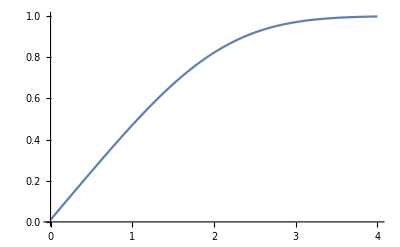

```mathematica
FigBlas=Plot[Evaluate[Vx[x,y  √(2x ν)]]/.x->XXX,{y,0,4}]
```

```mathematica
ω[x_,y_]:=(Vx[x,y+0.0001]-Vx[x,y])/0.0001
```

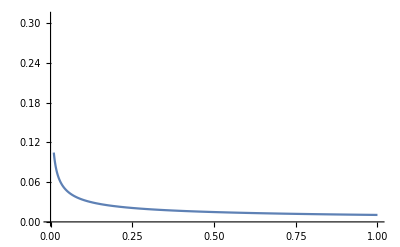

```mathematica
Plot[ν ω[x,0.001],{x,0.01,1},PlotRange->{0,0.31}]
```

```mathematica
Clear[ypod]
```

```mathematica
ypod[x_]:=Flatten[Solve[#,y]&/@Thread[(y /√(2x ν))==Range[0,4,0.01]],1];
tabl[x_]:={x-0.5,(y/.#)+halfh}&/@ypod[x];
```

```mathematica
SetDirectory@NotebookDirectory[]
```

C:\GitHub\VM2D\tutorials\blasius5k

```mathematica
flatTabl=Flatten[tabl[#]&/@Range[0.05,0.65,0.10],1]
```

{{-0.45,0.002},{-0.45,0.0021},{-0.45,0.0022},{-0.45,0.0023},{-0.45,0.0024},{-0.45,0.0025},{-0.45,0.0026},{-0.45,0.0027},{-0.45,0.0028},{-0.45,0.0029},2788,{0.15,0.143338},{0.15,0.143698},{0.15,0.144059},{0.15,0.144419},{0.15,0.14478},{0.15,0.14514},{0.15,0.145501},{0.15,0.145861},{0.15,0.146222}}
 |  |  |  |

```mathematica
Export["points.txt",flatTabl]
```

points.txt

```mathematica
ptsControl=Cases[flatTabl,{x_/;Abs[(x-(-0.5+XXX))]<10^-4,y_}];
```

```mathematica
ys=Cases[flatTabl,{x_/;Abs[(x-(-0.5+XXX))]<10^-4,y_}:>y];
```

```mathematica
posPtsControl=Flatten[Position[flatTabl,#]&/@ptsControl]
```

{803,804,805,806,807,808,809,810,811,812,813,814,815,816,817,818,819,820,821,822,823,824,825,826,827,828,829,830,831,832,833,834,835,836,837,838,839,840,841,842,843,844,845,846,847,848,849,850,851,852,853,854,855,856,857,858,859,860,861,862,863,864,865,866,867,868,869,870,871,872,873,874,875,876,877,878,879,880,881,882,883,884,885,886,887,888,889,890,891,892,893,894,895,896,897,898,899,900,901,902,903,904,905,906,907,908,909,910,911,912,913,914,915,916,917,918,919,920,921,922,923,924,925,926,927,928,929,930,931,932,933,934,935,936,937,938,939,940,941,942,943,944,945,946,947,948,949,950,951,952,953,954,955,956,957,958,959,960,961,962,963,964,965,966,967,968,969,970,971,972,973,974,975,976,977,978,979,980,981,982,983,984,985,986,987,988,989,990,991,992,993,994,995,996,997,998,999,1000,1001,1002,1003,1004,1005,1006,1007,1008,1009,1010,1011,1012,1013,1014,1015,1016,1017,1018,1019,1020,1021,1022,1023,1024,1025,1026,1027,1028,1029,1030,1031,1032,1033,1034,1035,1036,1037,1038,1039,1040,1041,1042,1043,1044,1045,1046,1047,1048,1049,1050,1051,1052,1053,1054,1055,1056,1057,1058,1059,1060,1061,1062,1063,1064,1065,1066,1067,1068,1069,1070,1071,1072,1073,1074,1075,1076,1077,1078,1079,1080,1081,1082,1083,1084,1085,1086,1087,1088,1089,1090,1091,1092,1093,1094,1095,1096,1097,1098,1099,1100,1101,1102,1103,1104,1105,1106,1107,1108,1109,1110,1111,1112,1113,1114,1115,1116,1117,1118,1119,1120,1121,1122,1123,1124,1125,1126,1127,1128,1129,1130,1131,1132,1133,1134,1135,1136,1137,1138,1139,1140,1141,1142,1143,1144,1145,1146,1147,1148,1149,1150,1151,1152,1153,1154,1155,1156,1157,1158,1159,1160,1161,1162,1163,1164,1165,1166,1167,1168,1169,1170,1171,1172,1173,1174,1175,1176,1177,1178,1179,1180,1181,1182,1183,1184,1185,1186,1187,1188,1189,1190,1191,1192,1193,1194,1195,1196,1197,1198,1199,1200,1201,1202,1203}

```mathematica
FromFile[pt_]:=Import["velPres/VP-atPoint-"<>ToString[pt]<>".csv"][[550;;,2]]
```

```mathematica
Vxs=Mean[FromFile[#-1]]&/@posPtsControl;
```

$Aborted

```mathematica
Max[Vxs]
```

1.03708

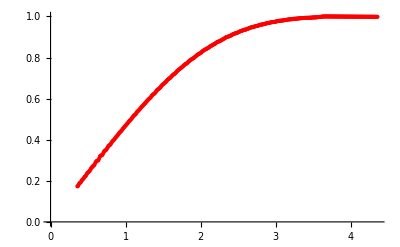

```mathematica
FigMy=ListPlot[Transpose[{Evaluate[(ys-halfh)/√(2x ν)/.x->XXX],Vxs/Max[Vxs]}],PlotStyle->Red]
```

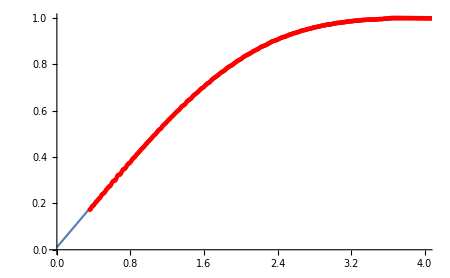

```mathematica
Show[FigBlas,FigMy]
```